```mathematica
a=({{1, 0, 0, 0, 0, 0, 0, 0, 0}, {(22500/(h^2)), (-(45000/(h^2))), (22500/(h^2)), 0, 0, 0, 0, 0, 0}, {0, (22500/(h^2)), (-(45000/(h^2))), (22500/(h^2)), 0, 0, 0, 0, 0}, {0, 0, (22500/(h^2)), (-(45000/(h^2))), (22500/(h^2)), 0, 0, 0, 0}, {0, 0, 0, (22500/(h^2)), (-(45000/(h^2))), (22500/(h^2)), 0, 0, 0}, {0, 0, 0, 0, (22500/(h^2)), (-(45000/(h^2))), (22500/(h^2)), 0, 0}, {0, 0, 0, 0, 0, (22500/(h^2)), (-(45000/(h^2))), (22500/(h^2)), 0}, {0, 0, 0, 0, 0, 0, (22500/(h^2)), (-(45000/(h^2))), (22500/(h^2))}, {0, 0, 0, 0, 0, 0, ((3*10000*2.25)/(2*h)), ((4*10000*2.25)/(2*h)), ((10000*2.25)/(2*h))}})
```

{{1,0,0,0,0,0,0,0,0},{22500/h^2,-45000/h^2,22500/h^2,0,0,0,0,0,0},{0,22500/h^2,-45000/h^2,22500/h^2,0,0,0,0,0},{0,0,22500/h^2,-45000/h^2,22500/h^2,0,0,0,0},{0,0,0,22500/h^2,-45000/h^2,22500/h^2,0,0,0},{0,0,0,0,22500/h^2,-45000/h^2,22500/h^2,0,0},{0,0,0,0,0,22500/h^2,-45000/h^2,22500/h^2,0},{0,0,0,0,0,0,22500/h^2,-45000/h^2,22500/h^2},{0,0,0,0,0,0,33750./h,45000./h,11250./h}}

```mathematica
b=({{0}, {-50}, {-50}, {-50}, {-50}, {-50}, {-50}, {-50}, {0}})
```

{{0},{-50},{-50},{-50},{-50},{-50},{-50},{-50},{0}}

```mathematica
(*let*)h=.1
```

0.1

```mathematica
LinearSolve[a,b]
```

{{2.35125×10^-19},{0.0000646091},{0.000106996},{0.00012716},{0.000125103},{0.000100823},{0.000054321},{-0.0000144033},{-0.00010535}}

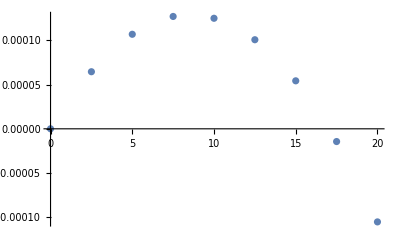

```mathematica
ListPlot[{{0,0},{2.5,0.0000646090534979426},{5,0.00010699588477366273},{7.5,0.00012716049382716064},{10,0.00012510288065843632},{12.5,0.00010082304526748978},{15,0.00005432098765432102},{17.5,-0.00001440329218106997},{20,-0.00010534979423868319}},PlotRange->All]
```

```mathematica
(*doesn't make much logical sense...*)
```